# Setup

## Imports

If not installed, run these commands to install QMeS and FormTracer:

```mathematica
Import["https://raw.githubusercontent.com/FormTracer/FormTracer/master/src/FormTracerInstaller.m"]
```

```mathematica
Import["https://raw.githubusercontent.com/QMeS-toolbox/QMeS-Derivation/main/QMeSInstaller.m"];
```

Load some local packages, for drawing Feynman Graphs, QMeS and FormTracer (and appropriate helpers and definitions)

```mathematica
SetDirectory[NotebookDirectory[]];
Get["DiFfRG.m"]
$Assumptions=q>0&&k>0&&p>0&&Nc>0;
```

FormTracer 2.3.7 loaded.

Copyright (C) 2013-2018, Anton K. Cyrol, Mario Mitter, Jan M. Pawlowski, and Nils Strodthoff.
FormTracer is released under the GNU General Public License version three or later.

If used in scientific publications, please acknowledge our work by citing:
A. K. Cyrol, M. Mitter, and N. Strodthoff, Comput. Phys. Commun. 219C (2017) 346-352, arXiv:1610.09331 [hep-ph]

Using FORM 4.2.0 (Jul  6 2017, v4.2.0) 64-bits.

Finite T disabled.

Lorentz structures are not disentangled.

Partial traces disabled.

Loaded DiFfRG Mathematica package
Author: Franz Richard Sattler (sattler@thphys.uni-heidelberg.de)
Version: 0.1
Year: 2024

## General setup

We need to define all used variables so that FormTracer does not complain .

```mathematica
AddExtraVars[
k,
(*regulators*)
RA,RAdot,Rc,Rcdot,

(*Angles for symmetric points*)
cosp1,cosp2,cosp3,

(*strong couplings*)
ZA3,ZA4,ZAcbc,

(*momentum variables*)
p1,p2,p3,p4,

(*propagators*)
GA,GAInv,m2A
];
```

If  you  want  to test some things, here are some explicit regulator definitions

```mathematica
LitimRegulators:={
RB[k2_,q2_]->(k2-q2)HeavisideTheta[k2-q2],
RBdot[k2_,q2_]->2k2 HeavisideTheta[k2-q2]
}
ExponentialRegulators[b_]:={
RB[k2_,q2_]->k2 Exp[-(q2/k2)^b],
RBdot[k2_,q2_]->2 ⅇ^(-(q2/k2)^b) k2 (1+b (q2/k2)^b)
}
Sn[d_]:=(2 π^(d/2))/Gamma[d/2]
```

## Tensors

Define  the  transverse/longitudinal projectors for gluons and the classical tensor structures.

```mathematica
DefineCombinedLorentzTensors[{
(*zero temperature*)
{
transProj[p,mu,nu],
deltaLorentz[mu,nu]-vec[p,mu]vec[p,nu]/sp[p,p]
},
{
transProj[p,q,mu,nu],
deltaLorentz[mu,nu]-vec[p,mu]vec[q,nu]/sp[p,q]
},
{
longProj[p,mu,nu],
vec[p,mu]vec[p,nu]/sp[p,p]
}
}];

DefineLorentzTensorIdentities[{
(*zero temperature*)
{transProj[p,mu,rho]transProj[p,rho,nu],transProj[p,mu,nu]},
{transProj[p,mu,rho]transProj[p,nu,rho],transProj[p,mu,nu]},
{transProj[p,rho,mu]transProj[p,rho,nu],transProj[p,mu,nu]},

{longProj[p,mu,rho]longProj[p,rho,nu],longProj[p,mu,nu]},
{longProj[p,mu,rho]longProj[p,nu,rho],longProj[p,mu,nu]},
{longProj[p,rho,mu]longProj[p,rho,nu],longProj[p,mu,nu]},

{transProj[p,mu,rho]longProj[p,rho,nu],0},
{transProj[p,rho,mu]longProj[p,rho,nu],0},
{transProj[p,mu,rho]longProj[p,nu,rho],0}
}];

ReplacementsLorentzTensors=Flatten[{
(*zero temperature*)
{transProj[p_,mu_,rho_]transProj[p_,rho_,nu_]:>transProj[p,mu,nu]},
{transProj[p_,mu_,rho_]transProj[p_,nu_,rho_]:>transProj[p,mu,nu]},
{transProj[p_,rho_,mu_]transProj[p_,rho_,nu_]:>transProj[p,mu,nu]},

{longProj[p_,mu_,rho_]longProj[p_,rho_,nu_]:>longProj[p,mu,nu]},
{longProj[p_,mu_,rho_]longProj[p_,nu_,rho_]:>longProj[p,mu,nu]},
{longProj[p_,rho_,mu_]longProj[p_,rho_,nu_]:>longProj[p,mu,nu]},

{transProj[p_,mu_,rho_]longProj[p_,rho_,nu_]:>0},
{transProj[p_,rho_,mu_]longProj[p_,rho_,nu_]:>0},
{transProj[p_,mu_,rho_]longProj[p_,nu_,rho_]:>0}
}];

InsertCombinedLorentzTensors[expr_]:=expr//.ReplacementsLorentzTensors//.{
transProj[p_,mu_,nu_]:>deltaLorentz[mu,nu]-vec[p,mu]vec[p,nu]/sp[p,p],
transProj[p_,q_,mu_,nu_]:>deltaLorentz[mu,nu]-vec[p,mu]vec[q,nu]/sp[p,q],
longProj[p_,mu_,nu_]:>vec[p,mu]vec[p,nu]/sp[p,p]
};
```

```mathematica
GlueTensors:={
PT[p_,v1_,a1_,v2_,a2_]:>transProj[p,v1,v2]deltaadjCol[a1,a2],
PL[p_,v1_,a1_,v2_,a2_]:>longProj[p,v1,v2]deltaadjCol[a1,a2],

(*Gluon Vertices*)
TAAA[p1_,v1_,a1_,p2_,v2_,a2_,p3_,v3_,a3_]:>ⅈ SUNFCol[a1,a2,a3] (deltaLorentz[v1,v2]vec[p2-p1,v3] +deltaLorentz[v1,v3] vec[p1-p3,v2] +deltaLorentz[v2,v3]vec[p3-p2,v1]),
TAAAA[p1_,v1_,a1_,p2_,v2_,a2_,p3_,v3_,a3_,p4_,v4_,a4_]:>(ff[a1,a2,a3,a4](deltaLorentz[v1,v3]deltaLorentz[v2,v4]-deltaLorentz[v1,v4]deltaLorentz[v2,v3])
											      +ff[a1,a3,a2,a4](deltaLorentz[v1,v2]deltaLorentz[v3,v4]-deltaLorentz[v1,v4]deltaLorentz[v2,v3])
											      +ff[a1,a4,a2,a3](deltaLorentz[v1,v2]deltaLorentz[v3,v4]-deltaLorentz[v1,v3]deltaLorentz[v2,v4])),
ff[ca_,cb_,cc_,cd_]:>Module[{i},SUNFCol[i,ca,cb]SUNFCol[i,cc,cd]],

(*Ghost-Gluon tensor structure*)
TAcbc[p1_,v1_,a1_,p2_,a2_,p3_,a3_]:>ⅈ  SUNFCol[a1,a2,a3] vec[p2,v1] 
};
```

## Feynman rules

We define in the following all Feynman rules needed to expand the QMeS expressions we obtain.
We split these into two categories: PreTraceRules and PostTraceRules. The PostTraceRules are not necessary for FormTracer, i.e. they carry no Tensor structure and thus can be applied after tracing. I do this simply to save RAM and time for the larger vertices, as this keeps the expressions minimal.

I  parametrize (for numerics) the glue propagator as 1/(Z_A p^2 + m_A^2). For the ghost, I absorb the wavefunction into the dressings; thus, only η_c =- 1/Z_c dZ_c/dt appears in the rules and also rescales the ghost-gluon dressing Z_Acbc  during the flow (see also below in the flow equations)

### Gluons

```mathematica
PostTraceRulesGluons:={
RAdot[p2_]:>ZA[(k^nZA+1)^(1/nZA)]RBdot[k^2,p2]+dtZA[(k^nZA+1)^(1/nZA)]RB[k^2,p2],
RA[p2_]:>ZA[(k^nZA+1)^(1/nZA)]RB[k^2,p2],
GA[p2_]:>1/(m2A+ZA[√p2] p2+ZA[(k^nZA+1)^(1/nZA)]RB[k^2,p2]),
GAInv[p2_]:>ZA[√p2]p2+m2A,
nZA:>6
}
```

```mathematica
PreTraceRulesGluons={
(*Regulators*)
RAA[{p1_,v1_,a1_,p2_,v2_,a2_}]:>RA[sp[p2,p2]]deltaadjCol[a1,a2]transProj[p2,v1,v2](*+ RA[sp[p2,p2]] 1/Xi PL[p2,v1,a1,v2,a2]*),

(*Regulator Derivatives*)
RdotAA[{p1_,v1_,a1_,p2_,v2_,a2_}]:>RAdot[sp[p2,p2]]deltaadjCol[a1,a2]transProj[p2,v1,v2](*+ RAdot[sp[p2,p2]] 1/Xi PL[p2,v1,a1,v2,a2]*),

(*Propagators*)
ΓAA[{p1_,v1_,a1_,p2_,v2_,a2_}] :> GAInv[sp[p2,p2]]deltaadjCol[a1,a2]transProj[p2,v1,v2](*+1/XiPL[p2,v1,a1,v2,a2]*),
GAA[{p1_,v1_,a1_,p2_,v2_,a2_}] :>GA[sp[p1,p1]]deltaadjCol[a1,a2]transProj[p1,v1,v2](*+Xi PL[p1,v1,a1,v2,a2]*),
(*Pure gauge Vertices*)
ΓAAA[{p1_,v1_,a1_,p2_,v2_,a2_,p3_,v3_,a3_}] :>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]))]TAAA[p1,v1,a1,p2,v2,a2,p3,v3,a3],
ΓAAAA[{p1_,v1_,a1_,p2_,v2_,a2_,p3_,v3_,a3_,p4_,v4_,a4_}] :>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[p4,p4]))] TAAAA[p1,v1,a1,p2,v2,a2,p3,v3,a3,p4,v4,a4],

(*Ghost-Gluon Vertices*)
ΓAcbc[{p1_,v1_,a1_,p2_,a2_,p3_,a3_}] :>ZAcbc[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]))] TAcbc[p1,v1,a1,p2,a2,p3,a3]
};

(*Must be 3(Nc^2-1)*)
FormTrace[(ΓAA[{p,v1,a1,-p,v2,a2}]+RAA[{p,v1,a1,-p,v2,a2}]) GAA[{-p,v2,a2,p1,v1,a1}]//.PreTraceRulesGluons//.GlueTensors]//.PostTraceRulesGluons//Simplify
```

3 (-1+Nc^2)

### Ghosts

```mathematica
PostTraceRulesGhosts:={
Rc[p2_]:>RB[k^2,p2],
Rcdot[p2_]:>RBdot[k^2,p2]- RB[k^2,p2]etac[√p2]
}
```

```mathematica
PreTraceRulesGhosts:={
(*Regulators*)
Rcbc[{p1_,a1_,p2_,a2_}]:>deltaadjCol[a1,a2] Rc[sp[p2,p2]],

(*Regulator Derivatives*)
Rdotcbc[{p1_,a1_,p2_,a2_}]:>deltaadjCol[a1,a2] Rcdot[sp[p2,p2]],

(*Propagators*)
Γcbc[{p1_,a1_,p2_,a2_}]:>-deltaadjCol[a1,a2]   sp[p2,p2],
Gccb[{p1_,a1_,p2_,a2_}]:>deltaadjCol[a1,a2]/(sp[p1,p1]+Rc[sp[p1,p1]])
}

(*Must be 1-Nc^2*)
FormTrace[(Γcbc[{-q,a1,q,a2}]-Rcbc[{-q,a1,q,a2}])Gccb[{q,a2,-q,a1}]//.PreTraceRulesGhosts]//.PostTraceRulesGhosts//Simplify
```

1-Nc^2

### All Feynman rules together

```mathematica
PreTraceRules:=PreTraceRulesGluons∪PreTraceRulesGhosts∪GlueTensors
PostTraceRules:=PostTraceRulesGhosts∪PostTraceRulesGluons
```

## fRG setup and truncation

Here, we set up QMeS. For more information, check the QMeS paper https://arxiv.org/abs/2102.01410

```mathematica
fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};

fields = <|"bosonic"-> { A[p,{v, c}]},
                 "fermionic"->{{cb[p,{c}],c[p,{c}]}}|>;

Truncation = {
{A,A},{cb,c},(* propagators *)
{cb,c,A},{A,A,A},{A,A,A,A}(* glue sector scatterings *)
};

SetupfRG = <|"MasterEquation"->fRGEq,
"FieldSpace"->fields,
"Truncation"->Truncation|>;
```

```mathematica
couplingsList:={
ZA3[__], ZA4[__], ZAcbc[__]
};
YMSimp[expr_]:=Collect[expr,couplingsList,Simplify];
SetStandardSimplify[YMSimp];
```

# Flows in Vaccum, 4D regulators

If  you scroll down, you can also see all the Feynman Diagrams contributing to each of the flow equations.

## Propagators

## Gluon propagator

```mathematica
(*Diagrams*)
DerivativeListAA= {A[-p,{v1,a1}],A[p,{v2,a2}]};
DiagramsAA =  AutoSaveRestore["diagrams/AA",DeriveFunctionalEquation[SetupfRG,DerivativeListAA,"OutputLevel"->"FullDiagrams"]];
Print["DiagramsAA got "<>ToString[Length[DiagramsAA]]<>" diagrams."]
```

Imported existing file "diagrams/AA.m"...

DiagramsAA got 7 diagrams.

#### m2A

```mathematica
(*Projection*)
Normm2A=PT[p,v1,a1,v2,a2]PT[p,v1,a1,v2,a2]//.PreTraceRules//FormTrace;
Projectorm2A=PT[p,v1,a1,v2,a2]/Normm2A;
(*Sanity Check*)
sanity=simplifyMomenta4D[q,p,(Projectorm2A ΓAA[{-p,v2,a2,p,v1,a1}]//.PreTraceRules//FormTrace//expandScalarProducts4D)]//.p->0//.PostTraceRules//Simplify;
Print["Projection check is ", sanity, ", should be m2A"]
```

Projection check is m2A, should be m2A

```mathematica
Projectionm2A=(Projectorm2A DiagramsAA)//.PreTraceRules//InsertCombinedLorentzTensors;
m2ALoop=1/2 Integrate[TracePropagator4D[8,"m2A",Projectionm2A,q,p]//.p->0,{cos1,-1,1}]//.PostTraceRules//Simplify
```

Tracing...

...done. Summing subterms...

...done.

4/9 Nc ((6 q^2 (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) q]^2)/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[q])^3)-(5 (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA4[q/(√2)])/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[q])^2)+(q^2 (etac[q] RB[k^2,q^2]-RBdot[k^2,q^2]) ZAcbc[√(2/3) q]^2)/((q^2+RB[k^2,q^2])^3))

#### ZA

```mathematica
(*Projection*)
NormZA=PT[p,v1,a1,v2,a2]PT[p,v1,a1,v2,a2]//.PreTraceRules//FormTrace;
ProjectorZA=PT[p,v1,a1,v2,a2]/NormZA;
(*Sanity Check*)
sanity=(ProjectorZA (ΓAA[{-p,v2,a2,p,v1,a1}]-ΓAA[{-q,v2,a2,q,v1,a1}])/sp[p,p]//.PreTraceRules//FormTrace//expandScalarProducts4D)//.{cos[p,q]->1,q->0}//.PostTraceRules//Simplify;
Print["Projection check is ", sanity, ", should be ZA[p]"]
```

Projection check is ZA[p], should be ZA[p]

```mathematica
ProjectionZA=(ProjectorZA DiagramsAA)//.PreTraceRules;
ZALoop=TracePropagator4D[4,"ZA",ProjectionZA,q,p];
ZALoop=Simplify[(ZALoop-(ZALoop//.p->0))/p^2]//.PostTraceRules
```

Tracing...

...done. Summing subterms...

...done.

1/(6 p^2)Nc (-(2 (-7+cos1^2) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA4[q/(√2)])/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2)+(2 (-7+cos1^2) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA4[(√(p^2+q^2))/(√2)])/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2)-((-1+cos1^2) q^2 (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) q]^2)/((q^2+RB[k^2,q^2])^3)-(-1+cos1^2) q^2 (-(12 (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) q]^2)/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^3)+((-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) q]^2)/((q^2+RB[k^2,q^2])^3))-2 (-1+cos1^2) q^2 (-(6 (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) q]^2)/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^3)+((-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) q]^2)/((q^2+RB[k^2,q^2])^3))+((-1+cos1^2) q^2 (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) √(p^2-cos1 p q+q^2)]^2)/((q^2+RB[k^2,q^2])^2 (p^2-2 cos1 p q+q^2+RB[k^2,p^2-2 cos1 p q+q^2]))+(-1+cos1^2) (-(4 (3 p^4+6 cos1 p^3 q+(8+cos1^2) p^2 q^2+6 cos1 p q^3+3 q^4) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(p^2+cos1 p q+q^2)]^2)/((p^2+2 cos1 p q+q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 cos1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cos1 p q+q^2) ZA[√(p^2+2 cos1 p q+q^2)]))+(q^2 (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) √(p^2-cos1 p q+q^2)]^2)/((q^2+RB[k^2,q^2])^2 (p^2-2 cos1 p q+q^2+RB[k^2,p^2-2 cos1 p q+q^2])))+(-1+cos1^2) (-(4 (3 p^4-6 cos1 p^3 q+(8+cos1^2) p^2 q^2-6 cos1 p q^3+3 q^4) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(p^2-cos1 p q+q^2)]^2)/((p^2-2 cos1 p q+q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2-2 cos1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2-2 cos1 p q+q^2) ZA[√(p^2-2 cos1 p q+q^2)]))+(2 q^2 (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) √(p^2+cos1 p q+q^2)]^2)/((q^2+RB[k^2,q^2])^2 (p^2+2 cos1 p q+q^2+RB[k^2,p^2+2 cos1 p q+q^2]))))

### Plotting

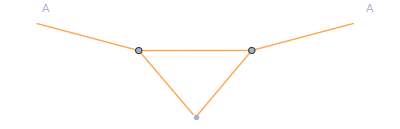
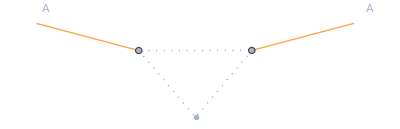
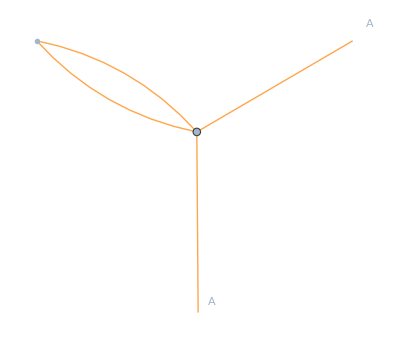
{{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-}}

```mathematica
PlotDiagrams[SetupfRG,{A[a],A[b]},{"AA"->Orange,"ccb"->Dotted}]
```

## Ghost propagator

```mathematica
(*Diagrams*)
DerivativeListcbc= {cb[-p,{a1}],c[p,{a2}]};
Diagramscbc =  AutoSaveRestore["diagrams/cbc", DeriveFunctionalEquation[SetupfRG,DerivativeListcbc,"OutputLevel"->"FullDiagrams"]];
Print["Diagramscbc got "<>ToString[Length[Diagramscbc]]<>" diagrams."]
```

Imported existing file "diagrams/cbc.m"...

Diagramscbc got 4 diagrams.

```mathematica
(*Projection*)
Normetac=deltaadjCol[a2,a1]  deltaadjCol[a1,a2]  //.PreTraceRules//FormTrace;
Projectoretac=-(-deltaadjCol[a2,a1])/Normetac;
(*Sanity Check*)
sanity=(Projectoretac Γcbc[{-p,a1,p,a2}]/sp[p,p]//.PreTraceRules//FormTrace//expandScalarProducts4D)//.PostTraceRules//Simplify;
Print["Projection check is ", sanity, ", should be -1"]
```

Projection check is -1, should be -1

```mathematica
Projectionetac=(Projectoretac Diagramscbc/sp[p,p])//.PreTraceRules;
etacLoop=TracePropagator4D[8,"etac",Projectionetac,q,p]//.PostTraceRules
```

Tracing...

...done. Summing subterms...

...done.

1/2 (-1+cos1^2) Nc ((2 q^2 (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) √(p^2-cos1 p q+q^2)]^2)/((p^2-2 cos1 p q+q^2) (q^2+RB[k^2,q^2])^2 (m2A+RB[k^2,p^2-2 cos1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2-2 cos1 p q+q^2) ZA[√(p^2-2 cos1 p q+q^2)]))+((dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ((ZAcbc[√(2/3) √(p^2-cos1 p q+q^2)]^2)/(p^2-2 cos1 p q+q^2+RB[k^2,p^2-2 cos1 p q+q^2])+(ZAcbc[√(2/3) √(p^2+cos1 p q+q^2)]^2)/(p^2+2 cos1 p q+q^2+RB[k^2,p^2+2 cos1 p q+q^2])))/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2))

### Plotting

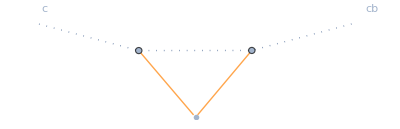
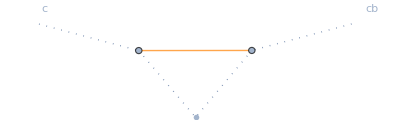
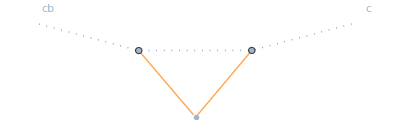
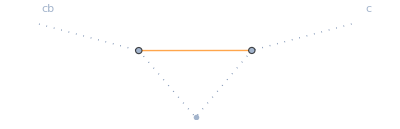
{{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-}}

```mathematica
Clear[a,b,c,d]
PlotDiagrams[SetupfRG,{cb[a],c[b]},{"AA"->Orange,"ccb"->Dotted,"cc"->Dotted,"cbcb"->Dotted}]
```

## Strong couplings

These  flows  are all projected to the symmetric point. cosp1, cosp2, ... are the angles between the internal loop momentum q and one of the external momenta p_n. Writing them like this is useful for directly translating into code - cosp1, ... are quite easily written down.

## Three-Gluon Vertex

```mathematica
(*Diagrams*)
DerivativeListA3= {A[p1,{v1,a1}],A[p2,{v2,a2}],A[p3,{v3,a3}]};
DiagramsA3=  AutoSaveRestore["diagrams/A3", DeriveFunctionalEquation[SetupfRG,DerivativeListA3,"OutputLevel"->"FullDiagrams"]];
Print["DiagramsAAA got "<>ToString[Length[DiagramsA3]]<>" diagrams."]
DiagramsA3=ProjectDiagramsToSymmetricPoint[DiagramsA3,SetupfRG,q,p1,p2,p3];
Print["DiagramsA3 reduces to "<>ToString[Length[DiagramsA3]]<>" diagrams on symmetric point."];
```

Saved to file "diagrams/A3.m"...

DiagramsAAA got 24 diagrams.

DiagramsA3 reduces to 4 diagrams on symmetric point.

```mathematica
(*Projection*)
NormZA3=(TAAA[p1,v1i,a1i,p2,v2i,a2i,p3,v3i,a3i]PT[p1,v1,a1,v1i,a1i]PT[p2,v2i,a2i,v2,a2]PT[p3,v3i,a3i,v3,a3]
TAAA[p1,v1,a1,p2,v2,a2,p3,v3,a3])//.PreTraceRules//FormTrace//Simplify;
ProjectorZA3=TAAA[p1,v1i,a1i,p2,v2i,a2i,p3,v3i,a3i]/NormZA3 PT[p1,v1,a1i,v1i,a1]PT[p2,v2i,a2i,v2,a2]PT[p3,v3i,a3i,v3,a3]//.PreTraceRules//Simplify;
(*Sanity check*)
sanity=Simplify[ProjectorZA3 ΓAAA[{p1,v1,a1,p2,v2,a2,p3,v3,a3}]//.PreTraceRules//FormTrace]//.{p1->p,p2->p,p3->p}//.PostTraceRules//expandScalarProducts4D//Simplify;
Print["Projection check is ", sanity, ", should be ZA3[p]"]
```

Projection check is ZA3[p], should be ZA3[p]

```mathematica
ProjectionZA3=(ProjectorZA3 DiagramsA3)//.PreTraceRules//InsertCombinedLorentzTensors;
ZA3LoopSP=TraceToSP4D[8,"ZA3",ProjectionZA3,q,p,p1,p2,p3]//.PostTraceRules
```

Tracing...

Lorentz structures are disentangled.

...done. Summing subterms...

...done.

1/66 Nc (1/((m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2)(dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ((2 (99 (-1+2 cosp1^2+2 cosp1 cosp2) p^7+231 (4 cosp1^3-cosp2+6 cosp1^2 cosp2+2 cosp1 (-1+cosp2^2)) p^6 q+3 (418 cosp1^4+836 cosp1^3 cosp2-6 (21+4 cosp2^2)+cosp1 cosp2 (51+16 cosp2^2)+cosp1^2 (51+434 cosp2^2)) p^5 q^2+2 (224 cosp1^5+560 cosp1^4 cosp2+16 cosp1^3 (60+17 cosp2^2)-8 cosp1^2 cosp2 (-180+19 cosp2^2)-cosp2 (241+64 cosp2^2)+cosp1 (-482+352 cosp2^2-88 cosp2^4)) p^4 q^3+2 (16 cosp1^6+48 cosp1^5 cosp2+cosp1^4 (622+20 cosp2^2)+cosp1^3 (1244 cosp2-40 cosp2^3)+cosp1^2 (163+218 cosp2^2-36 cosp2^4)-2 (93-14 cosp2^2+60 cosp2^4)+cosp1 (163 cosp2-404 cosp2^3-8 cosp2^5)) p^3 q^4+4 (52 cosp1^5+130 cosp1^4 cosp2+2 cosp1^3 (97+2 cosp2^2)+cosp1^2 (291 cosp2-124 cosp2^3)-2 cosp2 (18+25 cosp2^2+2 cosp2^4)-cosp1 (72+3 cosp2^2+58 cosp2^4)) p^2 q^5+12 (-6+16 cosp1^4+32 cosp1^3 cosp2+2 cosp2^2-8 cosp2^4+cosp1^2 (11-12 cosp2^2)+cosp1 (11 cosp2-28 cosp2^3)) p q^6+24 (2 cosp1^3+3 cosp1^2 cosp2-3 cosp1 cosp2^2-2 cosp2^3) q^7) ZA3[√(p^2+2/3 (2 cosp1+cosp2) p q+(2 q^2)/3)] ZA3[√(2/3) √(p^2+cosp1 p q+q^2)] ZA3[√(2/3) √(p^2+(cosp1+cosp2) p q+q^2)])/(p (p^2+2 cosp1 p q+q^2) (p^2+2 (cosp1+cosp2) p q+q^2) (m2A+RB[k^2,p^2+2 cosp1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp1 p q+q^2) ZA[√(p^2+2 cosp1 p q+q^2)]) (m2A+RB[k^2,p^2+2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2) p q+q^2)]))+(3 (-33 (-1+cosp2^2) p^2+cosp2 (54+4 cosp1^2+4 cosp1 cosp2-53 cosp2^2) p q+(54+4 cosp1^2+4 cosp1 cosp2-53 cosp2^2) q^2) ZA3[√(2/3) √(p^2+cosp2 p q+q^2)] ZA4[1/2 √(3 p^2+2 cosp2 p q+2 q^2)])/((p^2+2 cosp2 p q+q^2) (m2A+RB[k^2,p^2+2 cosp2 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp2 p q+q^2) ZA[√(p^2+2 cosp2 p q+q^2)])))-(3 (33 (-1+cosp1^2+2 cosp1 cosp2+cosp2^2) p^2+(-54 cosp1+53 cosp1^3-54 cosp2+163 cosp1^2 cosp2+163 cosp1 cosp2^2+53 cosp2^3) p q+(-54+53 cosp1^2+110 cosp1 cosp2+53 cosp2^2) q^2) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(p^2+(cosp1+cosp2) p q+q^2)] ZA4[1/2 √(3 p^2+2 (cosp1+cosp2) p q+2 q^2)])/((p^2+2 (cosp1+cosp2) p q+q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2) p q+q^2)]))-(2 q^2 ((-6+11 cosp1^2+11 cosp1 cosp2+2 cosp2^2) p+2 (-2 cosp1^3-3 cosp1^2 cosp2+3 cosp1 cosp2^2+2 cosp2^3) q) (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(p^2-2/3 (2 cosp1+cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2-cosp1 p q+q^2)] ZAcbc[√(2/3) √(p^2-(cosp1+cosp2) p q+q^2)])/(p (q^2+RB[k^2,q^2])^2 (p^2-2 cosp1 p q+q^2+RB[k^2,p^2-2 cosp1 p q+q^2]) (p^2-2 (cosp1+cosp2) p q+q^2+RB[k^2,p^2-2 (cosp1+cosp2) p q+q^2])))

### Plotting

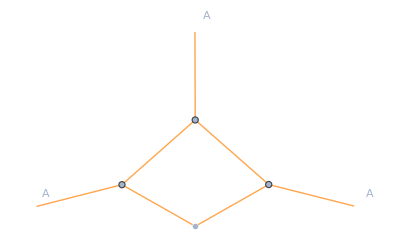
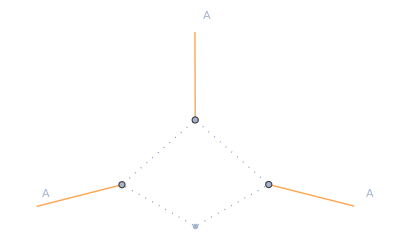
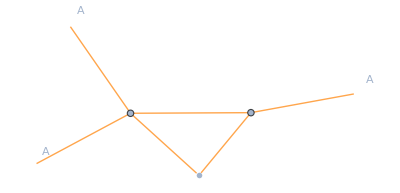
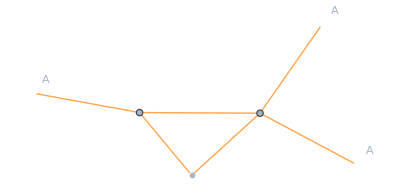
{{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-}}

```mathematica
PlotDiagrams[SetupfRG,{A[a],A[b],A[c]},{"AA"->Orange,"ccb"->Dotted,"cc"->Dotted,"cbcb"->Dotted}]
```

## Ghost-Gluon Vertex

```mathematica
(*Diagrams*)
DerivativeListAcbc={ A[p3,{v3,a3}],cb[p2,{a2}],c[p1,{a1}]};
DiagramsAcbc =  AutoSaveRestore["diagrams/Acbc", DeriveFunctionalEquation[SetupfRG,DerivativeListAcbc,"OutputLevel"->"FullDiagrams"]];
Print["DiagramsAcbc got "<>ToString[Length[DiagramsAcbc]]<>" diagrams."]
DiagramsAcbc=ProjectDiagramsToSymmetricPoint[DiagramsAcbc,SetupfRG,q,p1,p2,p3];
Print["DiagramsAcbc reduces to "<>ToString[Length[DiagramsAcbc]]<>" diagrams on symmetric point."];
```

Saved to file "diagrams/Acbc.m"...

DiagramsAcbc got 12 diagrams.

DiagramsAcbc reduces to 10 diagrams on symmetric point.

```mathematica
(*Projection*)
NormZAcbc=Simplify[TAcbc[p3,v3i,a3i,p1,a1,p2,a2]PT[p3,v3i,a3i,v3,a3]TAcbc[p3,v3,a3,p2,a2,p1,a1]//.PreTraceRules//FormTrace];
ProjectorZAcbc=(TAcbc[p3,v3i,a3i,p1,a1,p2,a2]PT[p3,v3i,a3i,v3,a3])/NormZAcbc;
(*Sanity check*)
sanity=Simplify[ProjectorZAcbc ΓAcbc[{p3,v3,a3,p2,a2,p1,a1}]//.PreTraceRules//FormTrace]//.{p1->p,p2->p,p3->p}//.PostTraceRules//expandScalarProducts4D//FullSimplify;
Print["Projection check is ", sanity, ", should be ZAcbc[p]"]
```

Projection check is ZAcbc[p], should be ZAcbc[p]

```mathematica
ProjectionAcbc=(ProjectorZAcbc DiagramsAcbc)//.PreTraceRules//InsertCombinedLorentzTensors;
ZAcbcSPLoop=TraceToSP4D[8,"ZAcbc",ProjectionAcbc,q,p,p1,p2,p3]//.PostTraceRules
ZAcbcRenorm=etac[p]ZAcbc[p]
```

Using result "/mnt/data/Documents/Uni/Code/fRG_Introduction_Code/YangMills//TraceBuffer/ZAcbc/result.m" from buffer...

-((1+2 cosp1 cosp2) Nc p (3 p+2 (cosp1-cosp2) q) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZAcbc[√(p^2+2/3 (cosp1-cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2+cosp1 p q+q^2)] ZAcbc[√(2/3) √(p^2-cosp2 p q+q^2)])/(24 (p^2+2 cosp1 p q+q^2+RB[k^2,p^2+2 cosp1 p q+q^2]) (p^2-2 cosp2 p q+q^2+RB[k^2,p^2-2 cosp2 p q+q^2]) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2)+ZA3[√(2/3) √(p^2-(cosp1+cosp2) p q+q^2)] ((Nc p ((-3+6 cosp1^2+6 cosp1 cosp2) p^3+(-14 cosp1^3+5 cosp2-24 cosp1^2 cosp2+cosp1 (7-10 cosp2^2)) p^2 q+2 (-3+6 cosp1^2+5 cosp1 cosp2+2 cosp1^3 cosp2+cosp2^2-2 cosp1 cosp2^3) p q^2+2 (cosp2-2 cosp1^2 cosp2+cosp1 (-1+2 cosp2^2)) q^3) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZAcbc[√(p^2-2/3 (2 cosp1+cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2-cosp1 p q+q^2)])/(12 (p^2-2 (cosp1+cosp2) p q+q^2) (p^2-2 cosp1 p q+q^2+RB[k^2,p^2-2 cosp1 p q+q^2]) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2-2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2-2 (cosp1+cosp2) p q+q^2) ZA[√(p^2-2 (cosp1+cosp2) p q+q^2)]))+(Nc p ((-3+6 cosp1 cosp2+6 cosp2^2) p^3+(7 cosp2-10 cosp1^2 cosp2-14 cosp2^3+cosp1 (5-24 cosp2^2)) p^2 q+2 (-3+cosp1^2-2 cosp1^3 cosp2+6 cosp2^2+cosp1 cosp2 (5+2 cosp2^2)) p q^2+2 (cosp1-cosp2+2 cosp1^2 cosp2-2 cosp1 cosp2^2) q^3) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZAcbc[√(p^2-2/3 (cosp1+2 cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2-cosp2 p q+q^2)])/(12 (p^2-2 (cosp1+cosp2) p q+q^2) (p^2-2 cosp2 p q+q^2+RB[k^2,p^2-2 cosp2 p q+q^2]) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2-2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2-2 (cosp1+cosp2) p q+q^2) ZA[√(p^2-2 (cosp1+cosp2) p q+q^2)])))+(Nc p q^2 ((-6+2 cosp1^2-7 cosp1 cosp2+2 cosp2^2) p^3+(9 cosp1-4 cosp1^3-9 cosp2+12 cosp1^2 cosp2-12 cosp1 cosp2^2+4 cosp2^3) p^2 q+(-9-4 cosp1^3 cosp2+6 cosp2^2+cosp1^2 (6+8 cosp2^2)+cosp1 (6 cosp2-4 cosp2^3)) p q^2+2 (cosp1-cosp2+2 cosp1^2 cosp2-2 cosp1 cosp2^2) q^3) (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZA3[√(p^2+2/3 (-cosp1+cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2-cosp1 p q+q^2)] ZAcbc[√(2/3) √(p^2+cosp2 p q+q^2)])/(6 (p^2-2 cosp1 p q+q^2) (p^2+2 cosp2 p q+q^2) (q^2+RB[k^2,q^2])^2 (m2A+RB[k^2,p^2-2 cosp1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2-2 cosp1 p q+q^2) ZA[√(p^2-2 cosp1 p q+q^2)]) (m2A+RB[k^2,p^2+2 cosp2 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp2 p q+q^2) ZA[√(p^2+2 cosp2 p q+q^2)]))+((1+2 cosp1 cosp2) Nc p (-3 p+2 (cosp1-cosp2) q) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZAcbc[√(p^2+2/3 (-cosp1+cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2-cosp1 p q+q^2)] ZAcbc[√(2/3) √(p^2+cosp2 p q+q^2)])/(24 (p^2-2 cosp1 p q+q^2+RB[k^2,p^2-2 cosp1 p q+q^2]) (p^2+2 cosp2 p q+q^2+RB[k^2,p^2+2 cosp2 p q+q^2]) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2)+ZA3[√(2/3) √(p^2+(cosp1+cosp2) p q+q^2)] ((Nc p ((-3+6 cosp1^2+6 cosp1 cosp2) p^3+(14 cosp1^3-5 cosp2+24 cosp1^2 cosp2+cosp1 (-7+10 cosp2^2)) p^2 q+2 (-3+6 cosp1^2+5 cosp1 cosp2+2 cosp1^3 cosp2+cosp2^2-2 cosp1 cosp2^3) p q^2+2 (cosp1-cosp2+2 cosp1^2 cosp2-2 cosp1 cosp2^2) q^3) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZAcbc[√(p^2+2/3 (2 cosp1+cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2+cosp1 p q+q^2)])/(12 (p^2+2 (cosp1+cosp2) p q+q^2) (p^2+2 cosp1 p q+q^2+RB[k^2,p^2+2 cosp1 p q+q^2]) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2) p q+q^2)]))+(Nc p ((-3+6 cosp1 cosp2+6 cosp2^2) p^3+(-5 cosp1-7 cosp2+10 cosp1^2 cosp2+24 cosp1 cosp2^2+14 cosp2^3) p^2 q+2 (-3+cosp1^2-2 cosp1^3 cosp2+6 cosp2^2+cosp1 cosp2 (5+2 cosp2^2)) p q^2+2 (cosp2-2 cosp1^2 cosp2+cosp1 (-1+2 cosp2^2)) q^3) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZAcbc[√(p^2+2/3 (cosp1+2 cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2+cosp2 p q+q^2)])/(12 (p^2+2 (cosp1+cosp2) p q+q^2) (p^2+2 cosp2 p q+q^2+RB[k^2,p^2+2 cosp2 p q+q^2]) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2) p q+q^2)])))+((cosp1-cosp2) Nc p q^2 (2 cosp2 p-q+cosp1 (p-2 cosp2 q)) (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(p^2-2/3 (2 cosp1+cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2-cosp1 p q+q^2)] ZAcbc[√(2/3) √(p^2-(cosp1+cosp2) p q+q^2)])/(6 (p^2-2 cosp1 p q+q^2) (q^2+RB[k^2,q^2])^2 (p^2-2 (cosp1+cosp2) p q+q^2+RB[k^2,p^2-2 (cosp1+cosp2) p q+q^2]) (m2A+RB[k^2,p^2-2 cosp1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2-2 cosp1 p q+q^2) ZA[√(p^2-2 cosp1 p q+q^2)]))+((-cosp1+cosp2) Nc p q^2 (cosp2 p+q+2 cosp1 (p+cosp2 q)) (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(p^2+2/3 (cosp1+2 cosp2) p q+(2 q^2)/3)] ZAcbc[√(2/3) √(p^2+cosp2 p q+q^2)] ZAcbc[√(2/3) √(p^2+(cosp1+cosp2) p q+q^2)])/(6 (p^2+2 cosp2 p q+q^2) (q^2+RB[k^2,q^2])^2 (p^2+2 (cosp1+cosp2) p q+q^2+RB[k^2,p^2+2 (cosp1+cosp2) p q+q^2]) (m2A+RB[k^2,p^2+2 cosp2 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp2 p q+q^2) ZA[√(p^2+2 cosp2 p q+q^2)]))

etac[p] ZAcbc[p]

### Plotting

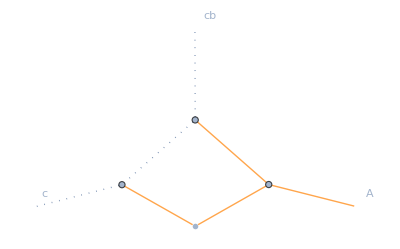
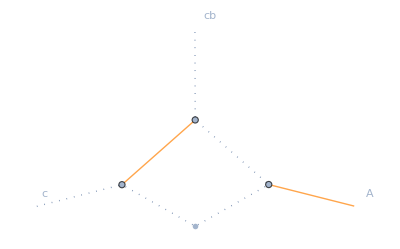
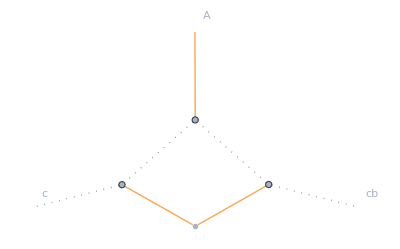
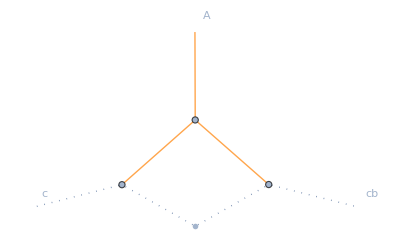
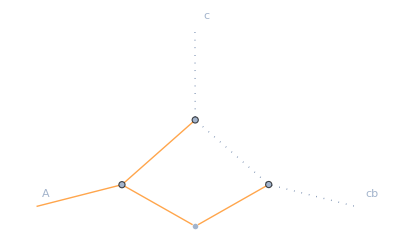
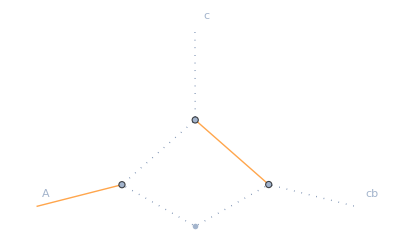
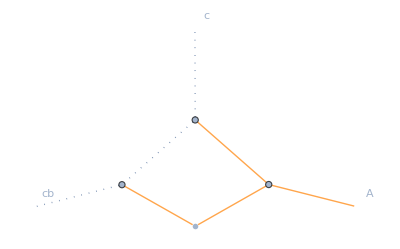
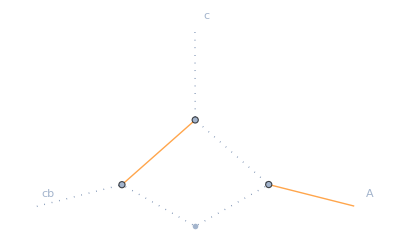
{{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-}}

```mathematica
Clear[a,b,c,d]
PlotDiagrams[SetupfRG,{A[a],cb[b],c[d]},{"AA"->Orange,"ccb"->Dotted,"cc"->Dotted,"cbcb"->Dotted}]
```

## Four-Gluon Vertex

```mathematica
(*Diagrams*)
DerivativeListA4= {A[p1,{v1,a1}],A[p2,{v2,a2}],A[p3,{v3,a3}],A[p4,{v4,a4}]};
DiagramsA4=AutoSaveRestore["diagrams/A4", DeriveFunctionalEquation[SetupfRG,DerivativeListA4,"OutputLevel"->"FullDiagrams"]];
Print["DiagramsA4 got "<>ToString[Length[DiagramsA4]]<>" diagrams."]
DiagramsA4=ProjectDiagramsToSymmetricPoint[DiagramsA4,SetupfRG,q,p1,p2,p3,p4];
Print["DiagramsA4 reduces to "<>ToString[Length[DiagramsA4]]<>" diagrams on symmetric point."];
```

Saved to file "diagrams/A4.m"...

DiagramsA4 got 114 diagrams.

DiagramsA4 reduces to 6 diagrams on symmetric point.

```mathematica
NormZA4=((TAAAA[p1,v1i,a1i,p2,v2i,a2i,p3,v3i,a3i,p4,v4i,a4i]PT[p1,v1,a1i,v1i,a1]PT[p2,v2i,a2i,v2,a2]PT[p3,v3i,a3i,v3,a3]PT[p4,v4i,a4i,v4,a4]//.PreTraceRules)TAAAA[p1,v1,a1,p2,v2,a2,p3,v3,a3,p4,v4,a4])//.PreTraceRules//InsertCombinedLorentzTensors//FormTrace//Simplify;
ProjectorZA4=1/NormZA4 TAAAA[p1,v1i,a1i,p2,v2i,a2i,p3,v3i,a3i,p4,v4i,a4i]PT[p1,v1,a1i,v1i,a1]PT[p2,v2i,a2i,v2,a2]PT[p3,v3i,a3i,v3,a3]PT[p4,v4i,a4i,v4,a4]//.PreTraceRules//Factor;
(*Sanity check*)
sanity=Simplify[ProjectorZA4  ΓAAAA[{p1,v1,a1,p2,v2,a2,p3,v3,a3,p4,v4,a4}]//.PreTraceRules//InsertCombinedLorentzTensors//FormTrace]//.{p1->p,p2->p,p3->p,p4->p}//.PostTraceRules//expandScalarProducts4D//Simplify;
Print["Projection check is ", sanity, ", should be ZA4[p]"]
```

Projection check is ZA4[p], should be ZA4[p]

Careful  here  about the parallelization, a single diagram may take up to 20GB RAM

```mathematica
ProjectionZA4=(ProjectorZA4 DiagramsA4)//.PreTraceRules//InsertCombinedLorentzTensors;
ZA4LoopSP=TraceToSP4D[1,"ZA4",ProjectionZA4,q,p,p1,p2,p3,p4]//.PostTraceRules
```

Tracing...

Lorentz structures are disentangled.

...done. Summing subterms...

...done.

-((8 Nc (1024 (-1+3 cosp1^2+3 cosp1 (cosp2+cosp3)) p^10+4 (5139 cosp1^3-1504 cosp2-209 cosp3+cosp1^2 (8547 cosp2+6870 cosp3)+3 cosp1 (-571+1136 cosp2^2+1713 cosp2 cosp3+577 cosp3^2)) p^9 q+2 (-2417+24486 cosp1^4-5684 cosp2^2-1599 cosp2 cosp3+1088 cosp3^2+42 cosp1^3 (1361 cosp2+971 cosp3)+cosp1^2 (-797+41226 cosp2^2+57621 cosp2 cosp3+16656 cosp3^2)+cosp1 (-7569 cosp2+8550 cosp2^3+5975 cosp3+17199 cosp2^2 cosp3+9009 cosp2 cosp3^2+360 cosp3^3)) p^8 q^2+2 (25038 cosp1^5+9 cosp1^4 (8431 cosp2+5479 cosp3)+3 cosp1^3 (8854+25497 cosp2^2+33738 cosp2 cosp3+7785 cosp3^2)-2 (3120 cosp2^3+928 cosp3+2706 cosp2^2 cosp3-312 cosp3^3+cosp2 (4357-591 cosp3^2))+cosp1^2 (25929 cosp2^3+47060 cosp3+53433 cosp2^2 cosp3-1350 cosp3^3+cosp2 (32626+24408 cosp3^2))+cosp1 (279 cosp2^4+1962 cosp2^3 cosp3-6 cosp2 cosp3 (-4658+201 cosp3^2)+cosp2^2 (448+909 cosp3^2)-2 (5285-7441 cosp3^2+216 cosp3^4))) p^7 q^3+(21960 cosp1^6+18 cosp1^5 (4591 cosp2+2729 cosp3)+9 cosp1^4 (11122+11526 cosp2^2+14695 cosp2 cosp3+2216 cosp3^2)-3 cosp1^2 (1808+5610 cosp2^4+8175 cosp2^3 cosp3-23280 cosp3^2+234 cosp3^4+24 cosp2^2 (-1541+163 cosp3^2)+6 cosp2 cosp3 (-12526+331 cosp3^2))+3 cosp1^3 (12144 cosp2^3+62164 cosp3+28635 cosp2^2 cosp3-2892 cosp3^3+23 cosp2 (3100+459 cosp3^2))-2 (3580+8901 cosp2^4+17010 cosp2^3 cosp3-2064 cosp3^2-774 cosp3^4+cosp2^2 (8871+7506 cosp3^2)+cosp2 (3027 cosp3-864 cosp3^3))-3 cosp1 (3402 cosp2^5+8847 cosp2^4 cosp3+37 cosp2^3 (200+189 cosp3^2)+2 cosp2^2 cosp3 (-1004+603 cosp3^2)+cosp2 (9098-8372 cosp3^2-594 cosp3^4)-2 cosp3 (2741+466 cosp3^2+126 cosp3^4))) p^6 q^4+3 (1728 cosp1^7-6642 cosp2^5-16623 cosp2^4 cosp3+18 cosp1^6 (409 cosp2+263 cosp3)+36 cosp2^2 cosp3 (-164+13 cosp3^2)+6 cosp1^5 (3548+1761 cosp2^2+2499 cosp2 cosp3+447 cosp3^2)-9 cosp2^3 (538+1241 cosp3^2)+2 cosp3 (-604+201 cosp3^2+342 cosp3^4)+cosp2 (-4448-510 cosp3^2+2664 cosp3^4)+3 cosp1^3 (5930-2784 cosp2^4-3882 cosp2^3 cosp3+5097 cosp3^2+708 cosp3^4+cosp2^2 (15661+42 cosp3^2)+2 cosp2 cosp3 (13202+771 cosp3^2))+3 cosp1^4 (702 cosp2^3+3507 cosp2^2 cosp3+3 cosp3 (5033+86 cosp3^2)+cosp2 (20381+2283 cosp3^2))+cosp1 (-5656-1728 cosp2^6-5184 cosp2^5 cosp3+7804 cosp3^2+3918 cosp3^4+54 cosp3^6+12 cosp2^3 cosp3 (-4139+45 cosp3^2)-3 cosp2^4 (9091+1377 cosp3^2)+6 cosp2 cosp3 (2636+808 cosp3^2+99 cosp3^4)+cosp2^2 (1106-20079 cosp3^2+1755 cosp3^4))+cosp1^2 (-7254 cosp2^5-17037 cosp2^4 cosp3+36 cosp2^2 cosp3 (59+111 cosp3^2)-3 cosp2^3 (4729+2886 cosp3^2)+2 cosp3 (15017+579 cosp3^2+540 cosp3^4)+cosp2 (23336+9603 cosp3^2+4275 cosp3^4))) p^5 q^5+3 (324 cosp1^8-3024 cosp2^6-9072 cosp2^5 cosp3+162 cosp1^7 (7 cosp2+9 cosp3)+9 cosp2^3 cosp3 (-1853+60 cosp3^2)+27 cosp1^6 (288+42 cosp2^2+155 cosp2 cosp3+84 cosp3^2)-27 cosp2^4 (313+273 cosp3^2)+6 cosp2 cosp3 (-116+228 cosp3^2+207 cosp3^4)+3 cosp2^2 (-392-2475 cosp3^2+1017 cosp3^4)+2 (-626+294 cosp3^2+675 cosp3^4+27 cosp3^6)+3 cosp1^4 (5509-1458 cosp2^4-1620 cosp2^3 cosp3+4095 cosp3^2+702 cosp3^4+15 cosp2^2 (533+57 cosp3^2)+15 cosp2 cosp3 (1045+123 cosp3^2))-18 cosp1^5 (72 cosp2^3-150 cosp2^2 cosp3-cosp3 (1166+135 cosp3^2)-2 cosp2 (713+150 cosp3^2))+3 cosp1^3 (-1458 cosp2^5-3087 cosp2^4 cosp3-72 cosp2^3 (75+19 cosp3^2)+3 cosp2^2 cosp3 (613+396 cosp3^2)+cosp3 (9617+3660 cosp3^2+324 cosp3^4)+cosp2 (12419+7281 cosp3^2+1305 cosp3^4))-3 cosp1 (108 cosp2^7+378 cosp2^6 cosp3+45 cosp2^4 cosp3 (368+3 cosp3^2)+12 cosp2^5 (593+36 cosp3^2)+cosp2^3 (4765+8328 cosp3^2-108 cosp3^4)-2 cosp3 (552+184 cosp3^2+513 cosp3^4)+cosp2^2 (5225 cosp3-4167 cosp3^3-108 cosp3^5)+cosp2 (72+1130 cosp3^2-4725 cosp3^4-27 cosp3^6))-3 cosp1^2 (648 cosp2^6+1854 cosp2^5 cosp3+36 cosp2^3 cosp3 (583+cosp3^2)+3 cosp2^4 (4507+528 cosp3^2)-3 cosp2^2 (1804-808 cosp3^2+231 cosp3^4)-cosp2 cosp3 (10039+8565 cosp3^2+378 cosp3^4)-3 (172+403 cosp3^2+1323 cosp3^4+18 cosp3^6))) p^4 q^6+9 (756 cosp1^7-108 cosp2^7-378 cosp2^6 cosp3+27 cosp1^6 (83 cosp2+113 cosp3)-45 cosp2^4 cosp3 (125+3 cosp3^2)-54 cosp2^5 (43+8 cosp3^2)+18 cosp1^5 (133+84 cosp2^2+406 cosp2 cosp3+219 cosp3^2)+9 cosp2^2 cosp3 (-106+129 cosp3^2+12 cosp3^4)+6 cosp2^3 (-86-507 cosp3^2+18 cosp3^4)+2 cosp3 (-56+3 cosp3^2+207 cosp3^4)+cosp2 (-176-498 cosp3^2+1638 cosp3^4+27 cosp3^6)+3 cosp1^3 (506-2727 cosp2^4-3456 cosp2^3 cosp3+467 cosp3^2+1089 cosp3^4+12 cosp2 cosp3 (237+232 cosp3^2)+cosp2^2 (1543+738 cosp3^2))+cosp1^4 (-3672 cosp2^3+5178 cosp3+2412 cosp2^2 cosp3+4077 cosp3^3+cosp2 (6792+8073 cosp3^2))-3 cosp1 (96+594 cosp2^6+1752 cosp2^5 cosp3+152 cosp3^2-874 cosp3^4-27 cosp3^6+6 cosp2^3 cosp3 (759+8 cosp3^2)+7 cosp2^4 (391+213 cosp3^2)+cosp2^2 (-318+873 cosp3^2-600 cosp3^4)-6 cosp2 cosp3 (32+273 cosp3^2+54 cosp3^4))-3 cosp1^2 (2052 cosp2^5+4449 cosp2^4 cosp3+8 cosp2^3 (253+255 cosp3^2)-3 cosp2^2 cosp3 (-411+482 cosp3^2)-cosp3 (524+1049 cosp3^2+342 cosp3^4)-cosp2 (994+810 cosp3^2+1629 cosp3^4))) p^3 q^7+27 (-16+333 cosp1^6-234 cosp2^6-702 cosp2^5 cosp3-28 cosp3^2+135 cosp3^4+9 cosp3^6+18 cosp1^5 (43 cosp2+68 cosp3)-36 cosp2^3 cosp3 (17+cosp3^2)-9 cosp2^4 (38+67 cosp3^2)+3 cosp1^4 (69+75 cosp2^2+740 cosp2 cosp3+450 cosp3^2)-3 cosp1^3 (-231 cosp2+552 cosp2^3-45 cosp3+44 cosp2^2 cosp3-724 cosp2 cosp3^2-492 cosp3^3)+cosp2 cosp3 (-10+189 cosp3^2+126 cosp3^4)+cosp2^2 (65-153 cosp3^2+225 cosp3^4)+3 cosp1^2 (13-849 cosp2^4-1208 cosp2^3 cosp3-106 cosp3^2+342 cosp3^4+cosp2^2 (173+24 cosp3^2)+cosp2 cosp3 (89+760 cosp3^2))-3 cosp1 (450 cosp2^5+18 cosp3+1024 cosp2^4 cosp3-77 cosp3^3-84 cosp3^5+4 cosp2^3 (37+131 cosp3^2)+cosp2^2 (146 cosp3-244 cosp3^3)+cosp2 (-44+23 cosp3^2-344 cosp3^4))) p^2 q^8+81 (54 cosp1^5-72 cosp2^5-180 cosp2^4 cosp3+90 cosp1^4 (cosp2+2 cosp3)+cosp2^3 (6-108 cosp3^2)-6 cosp1^3 (1+3 cosp2^2-36 cosp2 cosp3-27 cosp3^2)+3 cosp2^2 cosp3 (5+6 cosp3^2)+cosp1^2 (41 cosp2-252 cosp2^3-59 cosp3-138 cosp2^2 cosp3+192 cosp2 cosp3^2+198 cosp3^3)+2 cosp3 (-2+9 cosp3^4)+cosp2 (4-3 cosp3^2+54 cosp3^4)+cosp1 (-252 cosp2^4-408 cosp2^3 cosp3+192 cosp2 cosp3^3+cosp2^2 (53-54 cosp3^2)+cosp3^2 (-47+108 cosp3^2))) p q^9+243 (3 cosp1^4-6 cosp2^4-12 cosp2^3 cosp3+3 cosp1^3 (cosp2+3 cosp3)+cosp2^2 (2-3 cosp3^2)+cosp3^2 (-1+3 cosp3^2)+cosp2 cosp3 (2+3 cosp3^2)+cosp1^2 (-1-3 cosp2^2+5 cosp2 cosp3+6 cosp3^2)+cosp1 (2 cosp2-12 cosp2^3-4 cosp3-10 cosp2^2 cosp3+5 cosp2 cosp3^2+9 cosp3^3)) q^10) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(p^2+cosp1 p q+q^2)] ZA3[√(2/3) √(p^2+(cosp1+cosp2+cosp3) p q+q^2)] ZA3[1/3 √(10 p^2+6 (2 cosp1+cosp2) p q+6 q^2)] ZA3[1/3 √(10 p^2+6 (2 cosp1+2 cosp2+cosp3) p q+6 q^2)])/(441 (p^2+2 cosp1 p q+q^2) (p^2+2 (cosp1+cosp2+cosp3) p q+q^2) (4 p^2+6 (cosp1+cosp2) p q+3 q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 cosp1 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp1 p q+q^2) ZA[√(p^2+2 cosp1 p q+q^2)]) (m2A+RB[k^2,(4 p^2)/3+2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+((4 p^2)/3+2 (cosp1+cosp2) p q+q^2) ZA[√((4 p^2)/3+2 (cosp1+cosp2) p q+q^2)]) (m2A+RB[k^2,p^2+2 (cosp1+cosp2+cosp3) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2+cosp3) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2+cosp3) p q+q^2)])))+ZA3[√(2/3) √(p^2+(cosp1+cosp2+cosp3) p q+q^2)] ((Nc (392 (-1+3 cosp1 cosp2+3 cosp2^2+3 cosp2 cosp3) p^6+772 (3 cosp1^2 cosp2+6 cosp2^3-cosp3+9 cosp2^2 cosp3+cosp1 (-1+9 cosp2^2+6 cosp2 cosp3)+cosp2 (-2+3 cosp3^2)) p^5 q+2 (-682+102 cosp1^3 cosp2+2514 cosp2^4+5028 cosp2^3 cosp3+203 cosp3^2+cosp1^2 (203+2616 cosp2^2+234 cosp2 cosp3)+2 cosp2 cosp3 (454+51 cosp3^2)+4 cosp2^2 (227+654 cosp3^2)+cosp1 (5028 cosp2^3+382 cosp3+5160 cosp2^2 cosp3+cosp2 (908+234 cosp3^2))) p^4 q^2+(-99 cosp1^4 cosp2+1164 cosp2^5+2910 cosp2^4 cosp3+3 cosp1^3 (98+95 cosp2^2-210 cosp2 cosp3)+57 cosp2^2 cosp3 (196+5 cosp3^2)+6 cosp3 (-234+49 cosp3^2)+cosp2^3 (7448+2130 cosp3^2)+cosp2 (-2808+4312 cosp3^2-99 cosp3^4)+cosp1^2 (2130 cosp2^3+798 cosp3+153 cosp2^2 cosp3+cosp2 (4312-1062 cosp3^2))+cosp1 (-1404+2910 cosp2^4+3792 cosp2^3 cosp3+798 cosp3^2+3 cosp2^2 (3724+51 cosp3^2)+cosp2 (8456 cosp3-630 cosp3^3))) p^3 q^3+(-1072-27 cosp1^5 cosp2+54 cosp2^6+6372 cosp2^3 cosp3+162 cosp2^5 cosp3+402 cosp3^2-99 cosp3^4-9 cosp1^4 (11+6 cosp2^2+12 cosp2 cosp3)+27 cosp2^4 (118+5 cosp3^2)+cosp2^2 (1576+3579 cosp3^2-54 cosp3^4)+cosp2 (1576 cosp3+393 cosp3^3-27 cosp3^5)-3 cosp1^3 (210 cosp3+51 cosp2^2 cosp3+cosp2 (-131+45 cosp3^2))+3 cosp1^2 (134+45 cosp2^4+24 cosp2^3 cosp3-354 cosp3^2+cosp2^2 (1193-48 cosp3^2)+cosp2 (203 cosp3-45 cosp3^3))+cosp1 (162 cosp2^5+876 cosp3+306 cosp2^4 cosp3-630 cosp3^3+36 cosp2^3 (177+2 cosp3^2)-9 cosp2^2 cosp3 (-732+17 cosp3^2)+cosp2 (1576+609 cosp3^2-108 cosp3^4))) p^2 q^4-3 (9 cosp1^5-36 cosp2^5-90 cosp2^4 cosp3+9 cosp1^4 (3 cosp2+4 cosp3)-2 cosp2^3 (296+27 cosp3^2)+cosp1^3 (-6+9 cosp2^2+78 cosp2 cosp3+45 cosp3^2)+cosp2^2 (-888 cosp3+9 cosp3^3)+cosp3 (104-6 cosp3^2+9 cosp3^4)+cosp2 (208-308 cosp3^2+27 cosp3^4)-cosp1^2 (54 cosp2^3+42 cosp3+9 cosp2^2 cosp3-45 cosp3^3+cosp2 (308-66 cosp3^2))-cosp1 (-104+90 cosp2^4+132 cosp2^3 cosp3+42 cosp3^2-36 cosp3^4+cosp2^2 (888+9 cosp3^2)+cosp2 (664 cosp3-78 cosp3^3))) p q^5-3 (40+9 cosp1^4-18 cosp2^4-36 cosp2^3 cosp3-21 cosp3^2+9 cosp3^4+9 cosp1^3 (cosp2+3 cosp3)-3 cosp1^2 (7+3 cosp2^2-5 cosp2 cosp3-6 cosp3^2)+cosp2 cosp3 (-70+9 cosp3^2)-cosp2^2 (70+9 cosp3^2)-cosp1 (36 cosp2^3+30 cosp2^2 cosp3+cosp2 (70-15 cosp3^2)-27 cosp3 (-4+cosp3^2))) q^6) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(p^2+cosp2 p q+q^2)] ZA4[(√(2 p^2+(cosp1+2 cosp2+cosp3) p q+q^2))/(√2)])/(147 (p^2+2 cosp2 p q+q^2) (p^2+2 (cosp1+cosp2+cosp3) p q+q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 cosp2 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp2 p q+q^2) ZA[√(p^2+2 cosp2 p q+q^2)]) (m2A+RB[k^2,p^2+2 (cosp1+cosp2+cosp3) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2+cosp3) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2+cosp3) p q+q^2)]))+(Nc (8 (-584+843 cosp1^2+1686 cosp1 cosp2+843 cosp2^2+909 cosp1 cosp3+909 cosp2 cosp3+66 cosp3^2) p^6+2 (10869 cosp1^3+10869 cosp2^3+18015 cosp2^2 cosp3+3 cosp1^2 (11319 cosp2+6005 cosp3)-2 cosp3 (778+147 cosp3^2)+cosp2 (-9026+6852 cosp3^2)+cosp1 (-9026+33957 cosp2^2+37380 cosp2 cosp3+6852 cosp3^2)) p^5 q+3 (-4572+5724 cosp1^4+5724 cosp2^4+11559 cosp2^3 cosp3+3412 cosp3^2-1578 cosp3^4+3 cosp1^3 (8760 cosp2+3853 cosp3)+cosp2^2 (-488+2865 cosp3^2)+cosp1^2 (-488+41112 cosp2^2+40491 cosp2 cosp3+2865 cosp3^2)+cosp2 (7532 cosp3-4548 cosp3^3)+cosp1 (26280 cosp2^3+7532 cosp3+40491 cosp2^2 cosp3-4548 cosp3^3+cosp2 (44+8160 cosp3^2))) p^4 q^2+9 (72 cosp1^5+72 cosp2^5+3 cosp1^4 (458 cosp2-87 cosp3)-261 cosp2^4 cosp3+3 cosp1^3 (887+1266 cosp2^2+524 cosp2 cosp3-687 cosp3^2)-3 cosp2^3 (-887+687 cosp3^2)+cosp2^2 (6402 cosp3-2934 cosp3^3)-4 cosp3 (160+134 cosp3^2+9 cosp3^4)-2 cosp2 (1400-1397 cosp3^2+621 cosp3^4)+cosp1^2 (3798 cosp2^3+6402 cosp3+3702 cosp2^2 cosp3-2934 cosp3^3+cosp2 (9865-4173 cosp3^2))+cosp1 (-2800+1374 cosp2^4+1572 cosp2^3 cosp3+2794 cosp3^2-1242 cosp3^4+cosp2^2 (9865-4173 cosp3^2)-28 cosp2 cosp3 (-511+195 cosp3^2))) p^3 q^3-9 (54 cosp1^6+54 cosp2^6+135 cosp2^5 cosp3+135 cosp1^5 (2 cosp2+cosp3)+27 cosp2^4 (-13+2 cosp3^2)+9 cosp1^4 (-39+54 cosp2^2+58 cosp2 cosp3+6 cosp3^2)-9 cosp2^3 cosp3 (47+30 cosp3^2)+cosp2^2 (-473+2019 cosp3^2-459 cosp3^4)+cosp2 (-2050 cosp3+3012 cosp3^3-270 cosp3^5)+2 (508-661 cosp3^2+537 cosp3^4-27 cosp3^6)+9 cosp1^3 (60 cosp2^3+81 cosp2^2 cosp3+cosp2 (-392+cosp3^2)-cosp3 (47+30 cosp3^2))+cosp1^2 (-473+486 cosp2^4+729 cosp2^3 cosp3+2019 cosp3^2-459 cosp3^4-18 cosp2^2 (355+8 cosp3^2)-9 cosp2 cosp3 (547+106 cosp3^2))+cosp1 (270 cosp2^5-2050 cosp3+522 cosp2^4 cosp3+3012 cosp3^3-270 cosp3^5+9 cosp2^3 (-392+cosp3^2)-9 cosp2^2 cosp3 (547+106 cosp3^2)-2 cosp2 (776-1344 cosp3^2+477 cosp3^4))) p^2 q^4-9 (81 cosp1^5+81 cosp2^5+135 cosp2^4 cosp3+27 cosp1^4 (12 cosp2+5 cosp3)+9 cosp1^3 (-32+45 cosp2^2+42 cosp2 cosp3-3 cosp3^2)-9 cosp2^3 (32+3 cosp3^2)-6 cosp2^2 cosp3 (115+63 cosp3^2)+4 cosp3 (14+93 cosp3^2-27 cosp3^4)-2 cosp2 (-214+6 cosp3^2+189 cosp3^4)+3 cosp1^2 (135 cosp2^3+126 cosp2^2 cosp3-2 cosp3 (115+63 cosp3^2)-cosp2 (688+87 cosp3^2))+cosp1 (428+324 cosp2^4+378 cosp2^3 cosp3-12 cosp3^2-378 cosp3^4-12 cosp2 cosp3 (206+69 cosp3^2)-3 cosp2^2 (688+87 cosp3^2))) p q^5-27 (40+9 cosp1^4+9 cosp2^4+9 cosp2^3 cosp3-70 cosp3^2-18 cosp3^4+9 cosp1^3 (3 cosp2+cosp3)+3 cosp1^2 (-7+6 cosp2^2+5 cosp2 cosp3-3 cosp3^2)-3 cosp2^2 (7+3 cosp3^2)-2 cosp2 cosp3 (35+18 cosp3^2)+cosp1 (27 cosp2^3+15 cosp2^2 cosp3-6 cosp2 (18+5 cosp3^2)-2 cosp3 (35+18 cosp3^2))) q^6) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[1/3 √(10 p^2+6 (2 cosp1+2 cosp2+cosp3) p q+6 q^2)] ZA4[(√(5 p^2+3 (cosp1+cosp2) p q+3 q^2))/(√6)])/(441 (p^2+2 (cosp1+cosp2+cosp3) p q+q^2) (4 p^2+6 (cosp1+cosp2) p q+3 q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,(4 p^2)/3+2 (cosp1+cosp2) p q+q^2] ZA[(1+k^6)^(1/6)]+((4 p^2)/3+2 (cosp1+cosp2) p q+q^2) ZA[√((4 p^2)/3+2 (cosp1+cosp2) p q+q^2)]) (m2A+RB[k^2,p^2+2 (cosp1+cosp2+cosp3) p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 (cosp1+cosp2+cosp3) p q+q^2) ZA[√(p^2+2 (cosp1+cosp2+cosp3) p q+q^2)])))+(Nc (8 (-584+843 cosp2^2+777 cosp2 cosp3) p^6+2 (10869 cosp2^3-6 cosp2^2 (225 cosp1-2432 cosp3)-7470 cosp3-cosp2 (9026+1350 cosp1^2+1350 cosp1 cosp3-3429 cosp3^2)) p^5 q-3 (4572-5724 cosp2^4-11337 cosp2^3 cosp3+4608 cosp3^2+6 cosp1^2 (170+564 cosp2^2+159 cosp2 cosp3)+cosp2^2 (488-2532 cosp3^2)+3 cosp2 cosp3 (2836+501 cosp3^2)+6 cosp1 (564 cosp2^3+170 cosp3+723 cosp2^2 cosp3+cosp2 (170+159 cosp3^2))) p^4 q^2+9 (72 cosp2^5+cosp2^4 (-1014 cosp1+621 cosp3)-3 cosp2^3 (-887+326 cosp1^2+480 cosp1 cosp3+99 cosp3^2)-3 cosp3 (720+126 cosp1^2+126 cosp1 cosp3+137 cosp3^2)+cosp2 (-2800+36 cosp1^4+72 cosp1^3 cosp3-2027 cosp3^2-153 cosp3^4+20 cosp1 cosp3 (-113+9 cosp3^2)+2 cosp1^2 (-941+108 cosp3^2))+cosp2^2 (72 cosp1^3+1581 cosp3-354 cosp1^2 cosp3-963 cosp3^3-2 cosp1 (941+123 cosp3^2))) p^3 q^3+9 (-1016-54 cosp2^6-189 cosp2^5 cosp3-255 cosp3^2-153 cosp3^4+18 cosp1^4 (2+6 cosp2^2+3 cosp2 cosp3)-27 cosp2^4 (-13+7 cosp3^2)+cosp2^3 (981 cosp3-216 cosp3^3)+cosp2^2 (473-1182 cosp3^2-135 cosp3^4)-3 cosp2 cosp3 (368+297 cosp3^2+9 cosp3^4)+3 cosp1^2 (-202+18 cosp2^4+69 cosp2^3 cosp3+72 cosp3^2+24 cosp2^2 (-29+2 cosp3^2)+3 cosp2 cosp3 (-58+3 cosp3^2))+36 cosp1^3 (6 cosp2^3+2 cosp3+9 cosp2^2 cosp3+cosp2 (2+3 cosp3^2))-3 cosp1 (18 cosp2^5+202 cosp3+39 cosp2^4 cosp3-60 cosp3^3+cosp2^3 (708+45 cosp3^2)+cosp2^2 (906 cosp3+33 cosp3^3)+cosp2 (202+138 cosp3^2+9 cosp3^4))) p^2 q^4-9 (81 cosp2^5+27 cosp2^4 (3 cosp1+10 cosp3)-9 cosp2^3 (32+9 cosp1^2-18 cosp1 cosp3-27 cosp3^2)+3 cosp3 (124-18 cosp1^4-36 cosp1^3 cosp3+6 cosp3^2+9 cosp3^4-9 cosp1^2 (-4+cosp3^2)+9 cosp1 cosp3 (4+cosp3^2))-3 cosp2^2 (108 cosp1^3+58 cosp3+99 cosp1^2 cosp3-99 cosp3^3-20 cosp1 (20+3 cosp3^2))+cosp2 (428-162 cosp1^4-432 cosp1^3 cosp3+504 cosp3^2+162 cosp3^4+6 cosp1 cosp3 (218+21 cosp3^2)-3 cosp1^2 (-400+57 cosp3^2))) p q^5+27 (-40+18 cosp1^4-9 cosp2^4-27 cosp2^3 cosp3+21 cosp3^2-9 cosp3^4+36 cosp1^3 (cosp2+cosp3)-3 cosp2^2 (-7+6 cosp3^2)+cosp1^2 (-66+9 cosp2^2+30 cosp2 cosp3+9 cosp3^2)-cosp2 cosp3 (28+27 cosp3^2)-3 cosp1 (22 cosp2+3 cosp2^3+22 cosp3+5 cosp2^2 cosp3+5 cosp2 cosp3^2+3 cosp3^3)) q^6) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA3[√(2/3) √(p^2+cosp2 p q+q^2)] ZA3[1/3 √(10 p^2+6 (2 cosp2+cosp3) p q+6 q^2)] ZA4[(√(5 p^2+3 (cosp2+cosp3) p q+3 q^2))/(√6)])/(441 (p^2+2 cosp2 p q+q^2) (4 p^2+6 (cosp2+cosp3) p q+3 q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,p^2+2 cosp2 p q+q^2] ZA[(1+k^6)^(1/6)]+(p^2+2 cosp2 p q+q^2) ZA[√(p^2+2 cosp2 p q+q^2)]) (m2A+RB[k^2,(4 p^2)/3+2 (cosp2+cosp3) p q+q^2] ZA[(1+k^6)^(1/6)]+((4 p^2)/3+2 (cosp2+cosp3) p q+q^2) ZA[√((4 p^2)/3+2 (cosp2+cosp3) p q+q^2)]))+(Nc (16 (382+57 cosp1^2-9 cosp2^2-75 cosp2 cosp3-9 cosp3^2+57 cosp1 (cosp2+cosp3)) p^2+9 (cosp2+cosp3) (872+282 cosp1^2+151 cosp2^2+20 cosp2 cosp3+151 cosp3^2+282 cosp1 (cosp2+cosp3)) p q+3 (1304-54 cosp1^4+27 cosp2^4+81 cosp2^3 cosp3+399 cosp3^2+27 cosp3^4-108 cosp1^3 (cosp2+cosp3)-3 cosp1^2 (-262+9 cosp2^2+30 cosp2 cosp3+9 cosp3^2)+3 cosp2 cosp3 (4+27 cosp3^2)+cosp2^2 (399+54 cosp3^2)+3 cosp1 (262 cosp2+9 cosp2^3+262 cosp3+15 cosp2^2 cosp3+15 cosp2 cosp3^2+9 cosp3^3)) q^2) (dtZA[(1+k^6)^(1/6)] RB[k^2,q^2]+RBdot[k^2,q^2] ZA[(1+k^6)^(1/6)]) ZA4[(√(5 p^2+3 (cosp2+cosp3) p q+3 q^2))/(√6)]^2)/(588 (4 p^2+6 (cosp2+cosp3) p q+3 q^2) (m2A+RB[k^2,q^2] ZA[(1+k^6)^(1/6)]+q^2 ZA[√(q^2)])^2 (m2A+RB[k^2,(4 p^2)/3+2 (cosp2+cosp3) p q+q^2] ZA[(1+k^6)^(1/6)]+((4 p^2)/3+2 (cosp2+cosp3) p q+q^2) ZA[√((4 p^2)/3+2 (cosp2+cosp3) p q+q^2)]))+(Nc q^2 ((-16+43 cosp1^2+52 cosp1 cosp2+9 cosp2^2+34 cosp1 cosp3+6 cosp2 cosp3) p^2-3 (12 cosp1^3-18 cosp2^3-4 cosp3-21 cosp2^2 cosp3+6 cosp3^3+cosp1^2 (17 cosp2+19 cosp3)+cosp2 (4-3 cosp3^2)-cosp1 (7 cosp2^2+5 cosp3^2)) p q+9 (3 cosp1^4-6 cosp2^4-12 cosp2^3 cosp3+3 cosp1^3 (cosp2+3 cosp3)+cosp2^2 (2-3 cosp3^2)+cosp3^2 (-1+3 cosp3^2)+cosp2 cosp3 (2+3 cosp3^2)+cosp1^2 (-1-3 cosp2^2+5 cosp2 cosp3+6 cosp3^2)+cosp1 (2 cosp2-12 cosp2^3-4 cosp3-10 cosp2^2 cosp3+5 cosp2 cosp3^2+9 cosp3^3)) q^2) (-etac[√(q^2)] RB[k^2,q^2]+RBdot[k^2,q^2]) ZAcbc[√(2/3) √(p^2-cosp1 p q+q^2)] ZAcbc[√(2/3) √(p^2-(cosp1+cosp2+cosp3) p q+q^2)] ZAcbc[1/3 √(10 p^2-6 (2 cosp1+cosp2) p q+6 q^2)] ZAcbc[1/3 √(10 p^2-6 (2 cosp1+2 cosp2+cosp3) p q+6 q^2)])/(49 (q^2+RB[k^2,q^2])^2 (p^2-2 cosp1 p q+q^2+RB[k^2,p^2-2 cosp1 p q+q^2]) (4 p^2-6 (cosp1+cosp2) p q+3 q^2+3 RB[k^2,(4 p^2)/3-2 (cosp1+cosp2) p q+q^2]) (p^2-2 (cosp1+cosp2+cosp3) p q+q^2+RB[k^2,p^2-2 (cosp1+cosp2+cosp3) p q+q^2]))

### Plotting

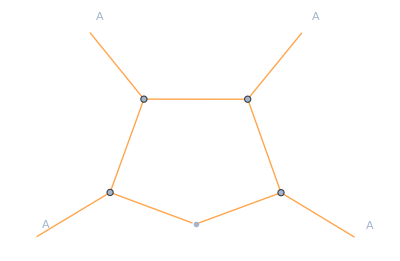
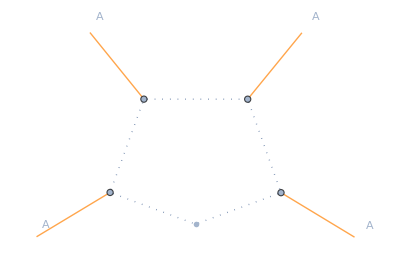
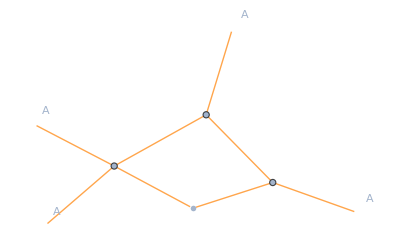
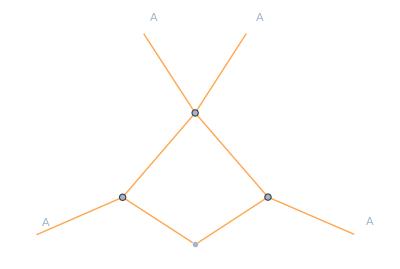
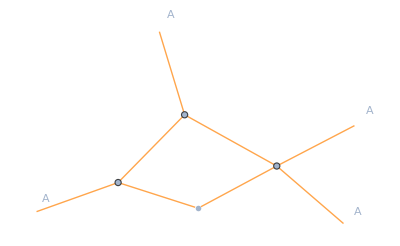
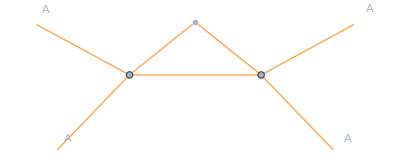
{{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-},{1/2,-Graphics-},{-1/2,-Graphics-},{-1/2,-Graphics-}}

```mathematica
PlotDiagrams[SetupfRG,{A[a],A[b],A[c],A[d]},{"AA"->Orange,"ccb"->Dotted,"cc"->Dotted,"cbcb"->Dotted}]
```